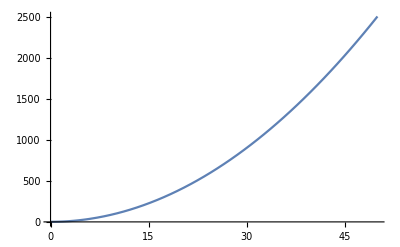

{I jtrs crd`sed sgd foql.1fnf embqypthnm in.1fsge woqkc,J!jsqs!drc_ree!sfc gpqk.1eng!elaqzquhml jo.1frfe!xopjc,K"jrps!esc^rff!seb hqqj.1dnh"el`pzrugll kp.1fqee"yooic,L#jqor"fsb]qfg"rda irqi.1cni#fk_p{svgkk!lp.1fpde#zonhb,M$jqnr#gtb\qgh#rca jsqhni$fj^o{tvfjj!mq.1foce${ongb,N%jpmr#hta[pgi#rb` ktqg.1anj%fj]o|uwfij!nr.1fnce%|omfb,N&jolr$itaZpgj$qa_!ltqg.19nk&fi\o|vwfhi"os.1embe%}oleb,O'knkq%ju`Yohk%q`^!muqf.18ml'gh[n}wxegh"ps.1elae&~okda,P(knjq%ku`Xohl%q_^!nvqe.17ml(ghZn}xxefh"qt.1ek`e'.7fpkca}

```mathematica
string = "I just created the form of encryption in the world";
changes={};
letters={};
answers = {};
Plot[x^2+1,{x,0,StringLength[string]}]
For [j = 1,j<10,j++,
For[i=1,i≤StringLength[string],i++,
changes=AppendTo[changes,Floor[j  Sin[i]]];
letters = AppendTo[letters,ToCharacterCode[StringPart[string,i]]]
];

letters = Flatten[letters];

letters = letters + changes;

SecretCode = FromCharacterCode[letters];

FromCharacterCode[ToCharacterCode[SecretCode]-changes];
answers= AppendTo[answers,SecretCode];
changes={};
letters={};
]

answers
```